```mathematica
data=Select[
Import["/home/nils/uni/Papers/2017/input-transformations/experiments/JTOBH.log","TSV"],
Length[#]>=11
&&#[[4]]==64
&&#[[5]]==2
&&#[[11]]>.65
&&#[[1]]=="0x15eed"
&&#[[12]]≠""
&
];
```

```mathematica
data =Table[
Join[row[[1;;11]],ToExpression/@StringSplit[row[[12]],","]],
{row,data}
];
```

```mathematica
groupedData=GroupBy[data,{#[[1]],#[[4]],#[[5]],#[[7]],#[[8]]}&];
```

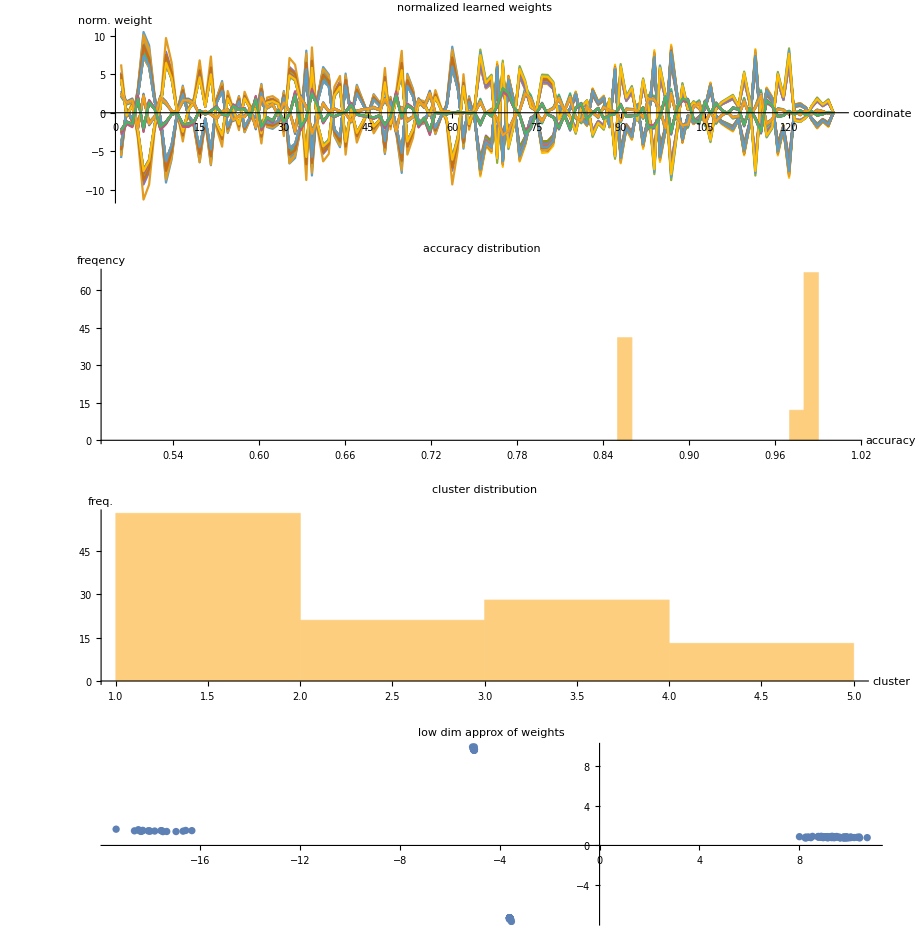

```mathematica
Table[
GraphicsGrid[
{
{
ListPlot[
groupedData[key][[All,12;;]],
ImageSize->Large,
AspectRatio->1/4,
Joined->True,
PlotLabel->"normalized learned weights",
AxesLabel->{"coordinate","norm. weight"}
]
},
{
Histogram[
groupedData[key][[All,11]],
{.5,1.01,.01},
ImageSize->Large,
AxesLabel->{"accuracy","freqency"},
PlotRange->Full,
AspectRatio->1/4,
PlotLabel->"accuracy distribution"
]
},
{
Histogram[
ClusteringComponents[groupedData[key][[All,12;;13]],Automatic,1],
{1},
AxesLabel->{"cluster","freq."},
ImageSize->Large,
PlotLabel->"cluster distribution",
AspectRatio->1/4,
PlotRange->Full
]
},
{
ListPlot[
DimensionReduce[groupedData[key][[All,12;;]],2],
PlotLabel->"low dim approx of weights",
ImageSize->Large,
AspectRatio->1/4,
PlotRange->Full
]
}
},
PlotLabel->ToString[key] <>", " <>ToString[Length[groupedData[key]]] <> " samples"
],
{key,Keys[groupedData]}
]
```